```mathematica
<<ACPackages`
```

```mathematica
SetWorkDir["2011.10.03\\Re1"]
```

d:\Home\Anton\programs\old\shellgrid(3dp)\2011.10.03\Re1

```mathematica
AverageTimeProfil[l_List,t_,dt_:1]:=Apply[Plus,#]/Length[#]&[Map[#[[2]]&,Select[lv,(t≤#[[1]][[1]]<t+dt)&]]];
```

```mathematica
AverageTimeProfil[l_List,t_]:=Apply[Plus,#]/Length[#]&[Map[#[[2]]&,Select[lv,(t≤#[[1]][[1]]<t+1)&]]];
```

## Чтение списков

```mathematica
Off[Thread::tdlen];
lv=ReadList["vv.dat"];lv=Map[Apply[List,#]&,lv];
ltm=Flatten[First/@lv];
{Length[ltm],Last[ltm]}
```

{526,0.812193}

```mathematica
Manipulate[ListLinePlot[lv⟦i,2⟧,PlotLabel->lv⟦i,1⟧,PlotRange->{0,1}],{i,1,Length[lv],1}]
```

```mathematica
PrintAnim[CutList[#[[2]]&/@lv,20]]
```

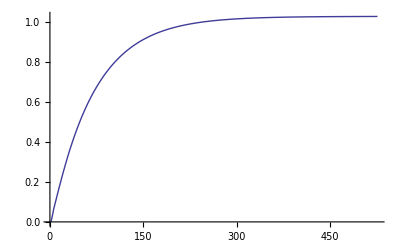

```mathematica
PrintRange[(Max[#1⟦2⟧]&)/@lv]
```

```mathematica
ListPlot[((Plus@@#1)/Length[#1]&)[Take[lv,{2000,4000}]],Joined->True,PlotRange->{0,1}]
```

```mathematica
ListPlot[AverageTimeProfil[lv,0,5],Joined->True]
```

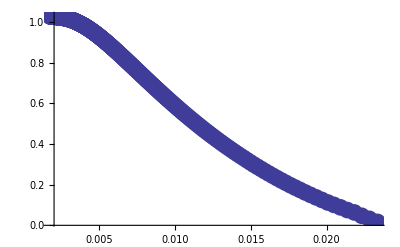
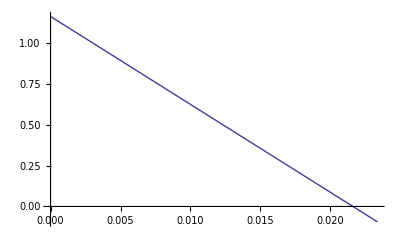

1.16096

```mathematica
ListLimit[(Max[#1⟦2⟧]&)/@lv,ApproximationReport->{LimitPlot}]
```

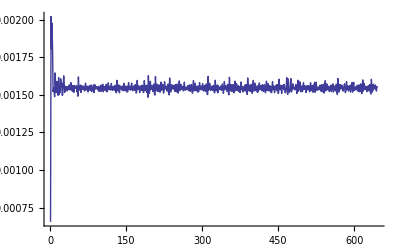

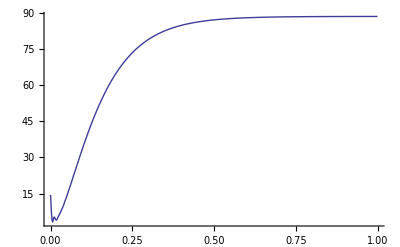

```mathematica
len=Import["energy.dat","Table"];
ltm=First/@len;PrintRange[dif[ltm]]
PrintRange[len]
```

```mathematica
lnu=ReadList["nut.dat"];
lnu=CutList[lnu,20];
ListPlot[#,PlotJoined->True,PlotRange->{0,Max[lnu]}]&/@lnu
```

### Структурные функции

```mathematica
ShowStruct[l_]:=Block[{gr},
gr=Table[ListPlot[10^l[[i]],PlotJoined->True,DisplayFunction->Identity,PlotStyle->{AbsoluteDashing[{4,i}]}],{i,1,4}];
Show[gr,DisplayFunction->$DisplayFunction];
];
```

```mathematica
lstr=ReadList["kaskvar.dat"]/.NAN->-∞;Length[lstr]
```

1302

```mathematica
ListPlot[nut=(∑_(i=1)^Length[#1] 10^(#1⟦i⟧) 4^-i&)[lstr⟦2⟧],Joined->True]
```

```mathematica
nut=Transpose[{Table[i,{i,-1,1,2./(Length[nut]-1)}],nut}];
```

```mathematica
ListPlot[nut,Joined->True]
```

```mathematica
NonlinearFit[nut,a E^(-x^2/c)+b,x,{a,b,c}]*1000//Simplify
```

0.391633+14.8007 ⅇ^(-2.13262 x^2)

```mathematica
(1/16)^(4/3)/10000.^(1/3)16^(2/3)*10000
```

73.1004

```mathematica
ShowStruct/@CutList[lstr,20];
```

## Чтение снимков

### Трёхмерные графики

```mathematica
{vx,vy,vz,p,nut}=ReadTextSnapFile["runtest_16000.snp",5];
```

{1,1,1}

{4.94776,16000,20,20,40,1.}

ghost=3

```mathematica
Max[Abs[#]]&/@{vx,vy,vz,p}
```

{1.0275,1.7598×10^-9,1.1157×10^-8,6.0933×10^-14}

```mathematica
ListPlot3D[#,PlotRange->All]&/@vx
```

```mathematica
Union@Flatten@nut
```

{0,1}

```mathematica
ListPlot3D[vx⟦4⟧,PlotRange->All]
```

```mathematica
{vx1,vy1,vz1,p1}={vx,vy,vz,p};
```

```mathematica
{vx2,vy2,vz2,p2}={vx,vy,vz,p};
```

```mathematica
Max/@{vx2-vx1,vy2-vy1,vz2-vz1,p2-p1}
```

{0.10888,0.,0.,0.}

```mathematica
ListPlot3D[#[[5]]&/@vx]
ListPlot3D[#[[5]]&/@vy]
ListPlot3D[#[[5]]&/@vz]
ListPlot3D[#[[5]]&/@p]
```

```mathematica
ListPlot3D[#[[5]]&/@vx1,ViewPoint->{-0.012, -3.220, 1.040}]
ListPlot3D[#[[5]]&/@vx2,ViewPoint->{-0.012, -3.220, 1.040}]
ListPlot3D[#[[5]]&/@(vx2-vx1),ViewPoint->{-0.012, -3.220, 1.040}]
```

### Каскадные переменные

```mathematica
Table[len[[i]],{i,Floor[count/20]-7,Length[len]}]
```

```mathematica
Table[ListPlot3D[vx[[k]],PlotLabel->k],{k,4,Length[vx]-4}];
```

```mathematica
lkask=ReadList["D:\\Home\\Anton\\3d\\kaskvar.dat"];Length[lkask]
```

315

```mathematica
lkask=(First[#]&/@Partition[lkask,10]);
```

```mathematica
lkask=Drop[lkask,{5,305}];
```

```mathematica
Off[Plot3D::gval];
ListPlot3D[#,ViewPoint->{21,-5,4},AxesLabel->{"layer","wave number",""},PlotRange->{-600,0}]&/@ReplacePart[lkask,-1000,Position[lkask,NAN]];
```